```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
μ0 = 3.82830;
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))];
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]];
```

```mathematica
mapRe[x_,y_,μ_] = x μ-x^2 μ+y^2 μ;
mapIm[x_,y_,μ_] = y μ-2 x y μ;
mapNormal[x_,μ_] = x μ (1-x);
```

```mathematica
listcomplex={};
For[i=0,i<100000,i++;
xn= RandomReal[{0,1}];
yn = RandomReal[{-0.01,0.01}];
For[n=0,n<3,n++;
{xnn,ynn} = {Re[map[xn,yn,μ0]],Im[map[xn,yn,μ0]]};
If[Abs[xnn]>100 , Break[]];
xn = xnn;
yn = ynn];
If[Abs[xnn]>100 , None,AppendTo[listcomplex, {xn,yn}]]];
```

```mathematica
listnormal={};
For[i=0,i<50000,i++;
xn= RandomReal[{0,1}];
For[n=0,n<1000,n++;
xnn = mapNormal[xn,μ0];
xn = xnn];
AppendTo[listnormal,xn]];
```

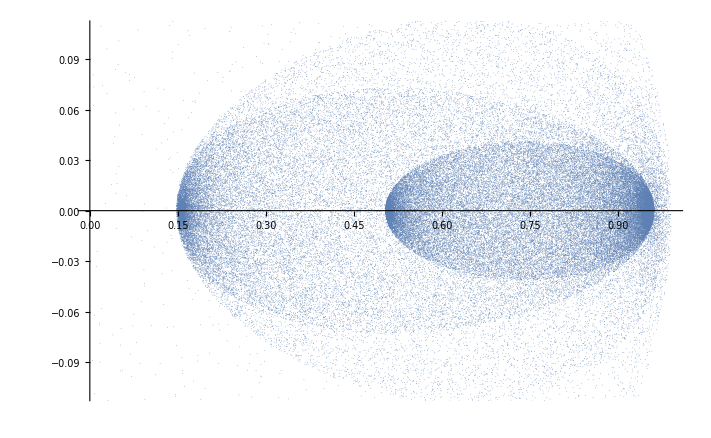

```mathematica
ListPlot[listcomplex,PlotRange-> Automatic, PlotStyle->PointSize[0.000001]]
```

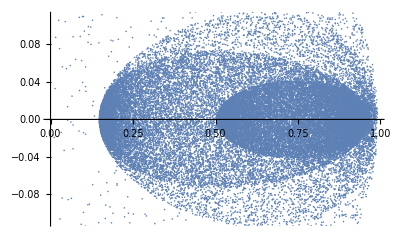

```mathematica
ListPlot[listcomplex,PlotRange-> Automatic]
```

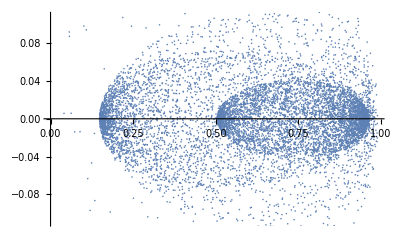

```mathematica
ListPlot[listcomplex,PlotRange-> Automatic]
```

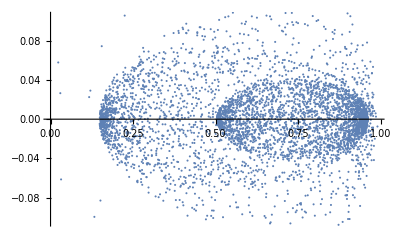

```mathematica
ListPlot[listcomplex,PlotRange-> Automatic]
```

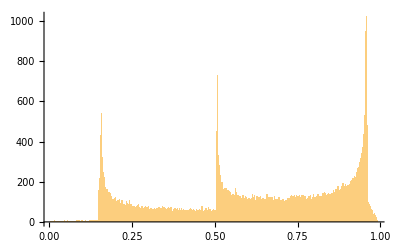

```mathematica
Histogram[listcomplex⟦All,1⟧, 1000]
```

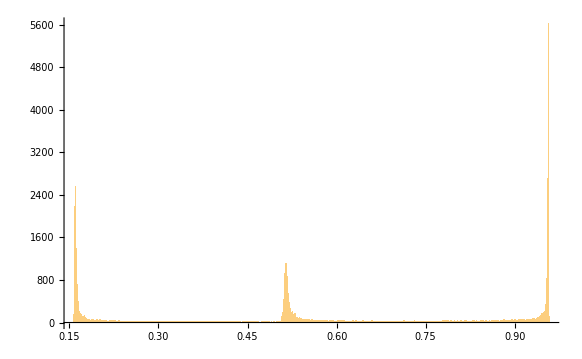

```mathematica
Histogram[listnormal,1000]
```